# Mean

```mathematica
getMeans[timepointStart_,timepointEnd_]:=Module[
{counts,countsA,countsB,countsC},
SetDirectory[NotebookDirectory[]];
countsA={};
countsB={};
countsC={};
Do[
counts=Import["../data_means/"<>IntegerString[timepoint,10,4]<>".txt","Table"];
AppendTo[countsA,{timepoint,counts[[1,2]]}];
AppendTo[countsB,{timepoint,counts[[2,2]]}];
AppendTo[countsC,{timepoint,counts[[3,2]]}];
,{timepoint,timepointStart,timepointEnd}];
Return[{countsA,countsB,countsC}]
];
```

```mathematica
means=getMeans[0,249];
```

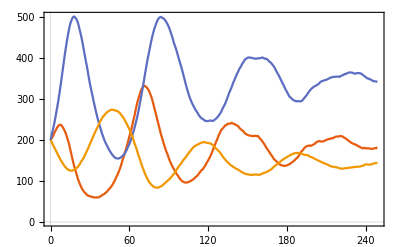

```mathematica
ListLinePlot[means]
```

```mathematica
ListPointPlot3D[Transpose[means[[;;,;;,2]]]]
```

-Graphics3D-

```mathematica
colDict=Association[];
colDict["A"]=RGBColor[0.81,0.0,0.79];
colDict["B"]=RGBColor[1.0,0.78,0.49];
colDict["C"]=RGBColor[0.52,0.96,1.0];
```

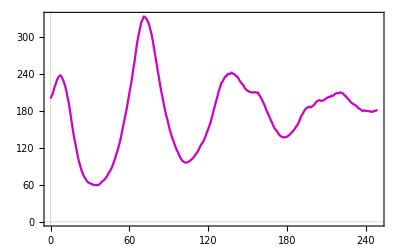

```mathematica
ListLinePlot[means[[1]],PlotStyle->colDict["A"]]
```

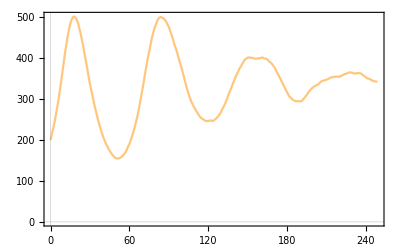

```mathematica
ListLinePlot[means[[2]],PlotStyle->colDict["B"]]
```

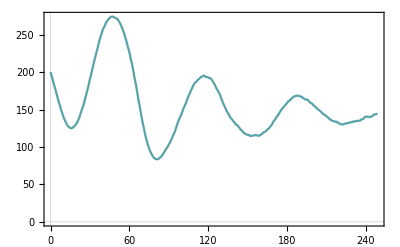

```mathematica
ListLinePlot[means[[3]],PlotStyle->Darker[colDict["C"]]]
```